## Seasonal Ricker Model with COEs

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/ricker_seasonal_coe/bifurcation"];
```

```mathematica
(* Import bifurcation data points *)
bifDataX= Import["../data_export/bif_data/bif_rb_x.csv"]; (* pop post breeding period *)

bifDataY= Import["../data_export/bif_data/bif_rb_y.csv"]; (* pop post non-breeding period *)
```

```mathematica
(* Paramters of model (from Betini et al.) *)
kb=224; (* Carrying capacity for breeding period *)
knb=-84.52;  (* Carrying capacity for non-breeding period *)
rnb=-0.0568 ; (* Growth rate for non-breeding period *)
a=0.0031; (* Regulates strength of COEs *)
```

### Population post-breeding period

```mathematica
(* Extract growth (r) values and state values *)
rValsX=bifDataX[[1,2;;]];
stateValsX=bifDataX[[2;;,2;;]];
```

```mathematica
(* Arrange for plotting *)
plotValsX=Table[Transpose[{rValsX,stateValsX[[i]]}],{i,1,Length[stateValsX]}];
```

```mathematica
bifRickerX=ListPlot[plotValsX[[1;;100]],
Frame->True,
FrameLabel->{{"Population size",None},{"Growth rate (r_b)",None}},
PlotRange->{{0.9,5},{0,500}},
PlotStyle->Directive[{TMBcolours[[1]],PointSize[0.002]}],
AspectRatio->0.5,
ImageSize->500,
LabelStyle->14];
```

```mathematica
stateValsX//Dimensions
```

{100,1000}

### Population post non-breeding period

```mathematica
(* Extract growth (r) values and state values *)
rValsY=bifDataY[[1,2;;]];
stateValsY=bifDataY[[2;;,2;;]];
```

```mathematica
(* Normalise state values by carrying capacity (of breeding period) *)
stateValsNormY=stateValsY/(kb);
```

```mathematica
(* Arrange for plotting *)
plotValsY=Table[Transpose[{rValsY,stateValsY[[i]]}],{i,1,Length[stateValsY]}];
```

```mathematica
bifRickerY=ListPlot[plotValsY[[1;;100]],
Frame->True,
FrameLabel->{{"Population size (N/K)",None},{"Growth rate (r_b)",None}},
PlotRange->{{0.9,5},{0,500}},
PlotStyle->Directive[{TMBcolours[[4]],PointSize[0.002]}],
AspectRatio->0.5,
ImageSize->500,
LabelStyle->14];
```

### Combine bifurcation plots

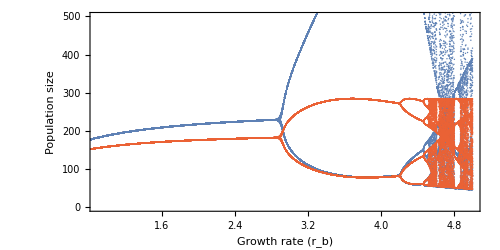

```mathematica
bifRickerComb=Show[bifRickerX,bifRickerY]
```

```mathematica
(*Export["../figures/bif_rb.png",bifRickerComb,ImageResolution->400];*)
```

### Find bifurcation points

```mathematica
(* Find max and min of state values *)
maxVals=Table[Max[stateValsX[[1;;,i]]],{i,1,Dimensions[stateValsX][[2]]}];
minVals=Table[Min[stateValsX[[1;;,i]]],{i,1,Dimensions[stateValsX][[2]]}];
```

```mathematica
(* Difference between max and min value *)
diff=maxVals-minVals;
```

```mathematica
diff//Dimensions
```

{1000}

```mathematica
(* Find the first position where diff > 0.01 *)
index=FirstPosition[diff,x_/;x>1][[1]]
```

522

```mathematica
(* First bifurcation value *)
bif1=rValsX[[index]]
```

2.84685